```mathematica
outputPath=StringJoin[NotebookDirectory[],"MagnetComparison/"];
cPath=NotebookDirectory[];
dataPath=StringJoin[NotebookDirectory[],"Experimental_Data/"];

fPath=NotebookDirectory[];
μ0=4*π*10^-7;

(* Globale Anweisung zur Darstellung von Plots *)
SetOptions[{Plot,ListLinePlot,LogPlot,LogLogPlot,ListPlot,ParametricPlot,ListLogLogPlot},PlotStyle->{{Thickness[0.005],{Blue}},{Thickness[0.005],{Red}},{Thickness[0.005],{Green}},{Thickness[0.005],{Magenta}},{Thickness[0.005],{Cyan}},{Thickness[0.005],{Orange}}},BaseStyle->{FontFamily->"Times",FontSize->13,Background->None,Black},GridLines->Automatic,Frame->True,FrameStyle->Black,Background->White,ImageSize->Medium,FrameTicksStyle->Background->None,LabelStyle->Background->None];

SetOptions[{StreamDensityPlot,RegionPlot,RegionPlot3D},PlotRange->All,PlotTheme->"Classic",AspectRatio->Automatic];
```

```mathematica
(* some auxiliary symbols *)
Q[k_]:={{Cos[α],0,-Sin[α]},{(-1)^k*Sin[α],0,(-1)^k*Cos[α]},{0,(-1)^(k+1),0}};
c[k_]:={Rm*Cos[α],Rm*(-1)^k*Sin[α],0}

xEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,1]])
yEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,2]])
zEigen[k_]:=({x,y,z}-c[k]).(Q[k][[All,3]])

X[k_,l_]:=xEigen[k]+(-1)^l*w
Y[k_,l_]:=yEigen[k]+(-1)^l*d
Z[k_]:=zEigen[k]

R[k_,l_,m_]:=Sqrt[X[k,l]^2+Y[k,m]^2+Z[k]^2]
```

```mathematica
(* potential *)
V=Sum[
(-1)^(k+l+m)*(
-Z[k]*ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]+X[k,l]*Log[Y[k,m]+R[k,l,m]]+Y[k,m]*Log[X[k,l]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
H=-Grad[V,{x,y,z}];
```

### Some derivatives

```mathematica
(* x *)
D[xEigen[k],x];
D[xEigen[k],y];
D[xEigen[k],z];
(* y *)
D[yEigen[k],x];
D[yEigen[k],y];
D[yEigen[k],z];
(* z *)
D[zEigen[k],x];
D[zEigen[k],y];
D[zEigen[k],z];
```

```mathematica
DXx[k_,l_]:=D[X[k,l],x];//Simplify
DXy[k_,l_]:=D[X[k,l],y];//Simplify
DXz[k_,l_]:=D[X[k,l],z];//Simplify
```

```mathematica
DYx[k_,l_]:=D[Y[k,l],x];//Simplify
DYy[k_,l_]:=D[Y[k,l],y];//Simplify
DYz[k_,l_]:=D[Y[k,l],z];//Simplify
```

```mathematica
DZx[k_]:=D[Z[k],x]; //Simplify
DZy[k_]:=D[Z[k],y];//Simplify
DZz[k_]:=D[Z[k],z];//Simplify
```

```mathematica
DRx[k_,l_,m_]:=D[R[k,l,m],x]; //Simplify
DRy[k_,l_,m_]:=D[R[k,l,m],y];//Simplify
DRz[k_,l_,m_]:=D[R[k,l,m],z];//Simplify
```

### Term by term

```mathematica
t1=Sum[
(-1)^(k+l+m)*(
-Z[k]*ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}]//Simplify;
```

```mathematica
t2=Sum[
(-1)^(k+l+m)*(
X[k,l]*Log[Y[k,m]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}]//Simplify;
```

```mathematica
t3=Sum[
(-1)^(k+l+m)*(
Y[k,m]*Log[X[k,l]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}]//Simplify;
```

### x

```mathematica
Dt11x=Sum[
(-1)^(k+l+m)*(
-DZx[k]*ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
Dt12x=Sum[
(-1)^(k+l+m)*(
- Z[k]*D[ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]], x]
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
Dt21x=Sum[
(-1)^(k+l+m)*(
DXx[k,l]*Log[Y[k,m]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
Dt22x=Sum[
(-1)^(k+l+m)*(
X[k,l]*D[Log[Y[k,m]+R[k,l,m]],x]
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
Dt31x=Sum[
(-1)^(k+l+m)*(
DYx[k,m]*Log[X[k,l]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}]
```

0

```mathematica
Dt32x=Sum[
(-1)^(k+l+m)*(
Y[k,m]*(DXx[k,l]+DRx[k,l,m])/(X[k,l]+R[k,l,m])
),
{k,1,2},{l,1,2},{m,1,2}];
```

### y

```mathematica
Dt11y=Sum[
(-1)^(k+l+m)*(
-DZy[k]*ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]] 
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
Dt12y=Sum[
(-1)^(k+l+m)*(
- Z[k]*D[ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]], y]
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
Dt21y=Sum[
(-1)^(k+l+m)*(
DXy[k,l]*Log[Y[k,m]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

(Log[d-z+√(d^2+Rm^2-2 Rm w+w^2+x^2+y^2-2 d z+z^2-2 (Rm-w) x Cos[α]-2 (Rm-w) y Sin[α])]-Log[-d-z+√(d^2+Rm^2-2 Rm w+w^2+x^2+y^2+2 d z+z^2-2 (Rm-w) x Cos[α]-2 (Rm-w) y Sin[α])]-Log[-d+z+√(d^2+Rm^2-2 Rm w+w^2+x^2+y^2-2 d z+z^2-2 (Rm-w) x Cos[α]+2 (Rm-w) y Sin[α])]+Log[d+z+√(d^2+Rm^2-2 Rm w+w^2+x^2+y^2+2 d z+z^2-2 (Rm-w) x Cos[α]+2 (Rm-w) y Sin[α])]-Log[d-z+√(d^2+Rm^2+2 Rm w+w^2+x^2+y^2-2 d z+z^2-2 (Rm+w) x Cos[α]-2 (Rm+w) y Sin[α])]+Log[-d-z+√(d^2+Rm^2+2 Rm w+w^2+x^2+y^2+2 d z+z^2-2 (Rm+w) x Cos[α]-2 (Rm+w) y Sin[α])]+Log[-d+z+√(d^2+Rm^2+2 Rm w+w^2+x^2+y^2-2 d z+z^2-2 (Rm+w) x Cos[α]+2 (Rm+w) y Sin[α])]-Log[d+z+√(d^2+Rm^2+2 Rm w+w^2+x^2+y^2+2 d z+z^2-2 (Rm+w) x Cos[α]+2 (Rm+w) y Sin[α])]) Sin[α]

```mathematica
Dt22y=Sum[
(-1)^(k+l+m)*(
X[k,l]*D[Log[Y[k,m]+R[k,l,m]],y]
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
Dt31y=Sum[
(-1)^(k+l+m)*(
DYy[k,m]*Log[X[k,l]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}]
```

0

```mathematica
Dt32y=Sum[
(-1)^(k+l+m)*(
Y[k,m]*(DXy[k,l]+DRy[k,l,m])/(X[k,l]+R[k,l,m])
),
{k,1,2},{l,1,2},{m,1,2}];
```

### z

```mathematica
Dt11z=Sum[
(-1)^(k+l+m)*(
-DZz[k]*ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]] 
),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

0

```mathematica
Dt12z=Sum[
(-1)^(k+l+m)*(
- Z[k]*D[ArcTan[X[k,l]*Y[k,m]/Z[k]/R[k,l,m]],z]
),
{k,1,2},{l,1,2},{m,1,2}];
```

```mathematica
Dt21z=Sum[
(-1)^(k+l+m)*(
DXz[k,l]*Log[Y[k,m]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}]
```

0

```mathematica
Dt22z=Sum[
(-1)^(k+l+m)*(
X[k,l]*D[Log[Y[k,m]+R[k,l,m]],z]
),
{k,1,2},{l,1,2},{m,1,2}]//Simplify;
```

```mathematica
Dt31z=Sum[
(-1)^(k+l+m)*(
DYz[k,m]*Log[X[k,l]+R[k,l,m]]
),
{k,1,2},{l,1,2},{m,1,2}]//Simplify
```

-Log[-Rm+w+x Cos[α]+y Sin[α]+√(d^2+Rm^2-2 Rm w+w^2+x^2+y^2-2 d z+z^2-2 (Rm-w) x Cos[α]-2 (Rm-w) y Sin[α])]+Log[-Rm+w+x Cos[α]+y Sin[α]+√(d^2+Rm^2-2 Rm w+w^2+x^2+y^2+2 d z+z^2-2 (Rm-w) x Cos[α]-2 (Rm-w) y Sin[α])]+Log[-Rm+w+x Cos[α]-y Sin[α]+√(d^2+Rm^2-2 Rm w+w^2+x^2+y^2-2 d z+z^2-2 (Rm-w) x Cos[α]+2 (Rm-w) y Sin[α])]-Log[-Rm+w+x Cos[α]-y Sin[α]+√(d^2+Rm^2-2 Rm w+w^2+x^2+y^2+2 d z+z^2-2 (Rm-w) x Cos[α]+2 (Rm-w) y Sin[α])]+Log[-Rm-w+x Cos[α]+y Sin[α]+√(d^2+Rm^2+2 Rm w+w^2+x^2+y^2-2 d z+z^2-2 (Rm+w) x Cos[α]-2 (Rm+w) y Sin[α])]-Log[-Rm-w+x Cos[α]+y Sin[α]+√(d^2+Rm^2+2 Rm w+w^2+x^2+y^2+2 d z+z^2-2 (Rm+w) x Cos[α]-2 (Rm+w) y Sin[α])]-Log[-Rm-w+x Cos[α]-y Sin[α]+√(d^2+Rm^2+2 Rm w+w^2+x^2+y^2-2 d z+z^2-2 (Rm+w) x Cos[α]+2 (Rm+w) y Sin[α])]+Log[-Rm-w+x Cos[α]-y Sin[α]+√(d^2+Rm^2+2 Rm w+w^2+x^2+y^2+2 d z+z^2-2 (Rm+w) x Cos[α]+2 (Rm+w) y Sin[α])]

```mathematica
Dt32z=Sum[
(-1)^(k+l+m)*(
Y[k,m]*(DXz[k,l]+DRz[k,l,m])/(X[k,l]+R[k,l,m])
),
{k,1,2},{l,1,2},{m,1,2}]
```

-((-d-z)^2/(√((-d-z)^2+(-(x-Rm Cos[α]) Sin[α]+Cos[α] (y-Rm Sin[α]))^2+(-w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α]))^2) (-w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α])+√((-d-z)^2+(-(x-Rm Cos[α]) Sin[α]+Cos[α] (y-Rm Sin[α]))^2+(-w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α]))^2))))+(d-z)^2/(√((d-z)^2+(-(x-Rm Cos[α]) Sin[α]+Cos[α] (y-Rm Sin[α]))^2+(-w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α]))^2) (-w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α])+√((d-z)^2+(-(x-Rm Cos[α]) Sin[α]+Cos[α] (y-Rm Sin[α]))^2+(-w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α]))^2)))+(-d-z)^2/(√((-d-z)^2+(-(x-Rm Cos[α]) Sin[α]+Cos[α] (y-Rm Sin[α]))^2+(w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α]))^2) (w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α])+√((-d-z)^2+(-(x-Rm Cos[α]) Sin[α]+Cos[α] (y-Rm Sin[α]))^2+(w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α]))^2)))-(d-z)^2/(√((d-z)^2+(-(x-Rm Cos[α]) Sin[α]+Cos[α] (y-Rm Sin[α]))^2+(w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α]))^2) (w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α])+√((d-z)^2+(-(x-Rm Cos[α]) Sin[α]+Cos[α] (y-Rm Sin[α]))^2+(w+Cos[α] (x-Rm Cos[α])+Sin[α] (y-Rm Sin[α]))^2)))-(-d+z)^2/(√((-d+z)^2+(-(x-Rm Cos[α]) Sin[α]-Cos[α] (y+Rm Sin[α]))^2+(-w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α]))^2) (-w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α])+√((-d+z)^2+(-(x-Rm Cos[α]) Sin[α]-Cos[α] (y+Rm Sin[α]))^2+(-w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α]))^2)))+(d+z)^2/(√((d+z)^2+(-(x-Rm Cos[α]) Sin[α]-Cos[α] (y+Rm Sin[α]))^2+(-w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α]))^2) (-w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α])+√((d+z)^2+(-(x-Rm Cos[α]) Sin[α]-Cos[α] (y+Rm Sin[α]))^2+(-w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α]))^2)))+(-d+z)^2/(√((-d+z)^2+(-(x-Rm Cos[α]) Sin[α]-Cos[α] (y+Rm Sin[α]))^2+(w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α]))^2) (w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α])+√((-d+z)^2+(-(x-Rm Cos[α]) Sin[α]-Cos[α] (y+Rm Sin[α]))^2+(w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α]))^2)))-(d+z)^2/(√((d+z)^2+(-(x-Rm Cos[α]) Sin[α]-Cos[α] (y+Rm Sin[α]))^2+(w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α]))^2) (w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α])+√((d+z)^2+(-(x-Rm Cos[α]) Sin[α]-Cos[α] (y+Rm Sin[α]))^2+(w+Cos[α] (x-Rm Cos[α])-Sin[α] (y+Rm Sin[α]))^2)))

Check with standard formulation

```mathematica
D[V,x]-Dt11x-Dt12x-Dt21x-Dt22x-Dt31x-Dt32x//Simplify
```

0

```mathematica
D[V,y]-Dt11y-Dt12y-Dt21y-Dt22y-Dt31y-Dt32y//Simplify
```

0

```mathematica
D[V,z]-Dt11z-Dt12z-Dt21z-Dt22z-Dt31z-Dt32z//Simplify
```

0

### Plot

```mathematica
padx=2;
pady=2;

wVal=1/2;
dVal=1/2;

αVal=π/4;
RmVal=4;

pars={w->wVal,d->dVal,z->0, α->αVal,Rm->RmVal};
Hplot[x_,y_]=H/.pars;
```

```mathematica
padR=1;
canvas=Rectangle[{0,-RmVal},{2RmVal,RmVal}];

magnetSegment=RegionDifference[Disk[{0,0},RmVal+wVal,{-αVal,αVal}],
Disk[{0,0},RmVal-wVal,{-αVal,αVal}]];
```

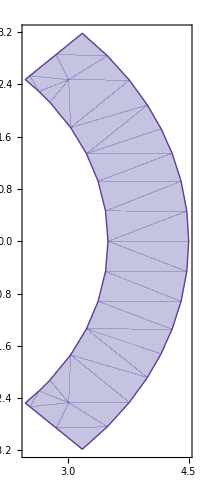

```mathematica
RegionPlot[magnetSegment,AspectRatio->Automatic]
```

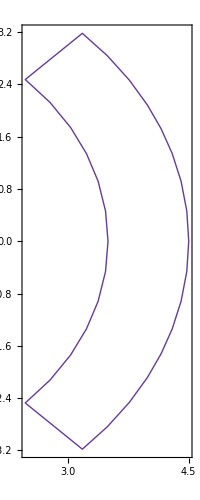

```mathematica
magnetSegmentBoundary =RegionUnion[
Circle[{0,0},RmVal+wVal,{-αVal,αVal}],
Circle[{0,0},RmVal-wVal,{-αVal,αVal}],
Line[{{(RmVal-wVal)*Cos[αVal],(RmVal-wVal)*Sin[αVal]},{(RmVal+wVal)*Cos[αVal],(RmVal+wVal)*Sin[αVal]}}],
Line[{{(RmVal-wVal)*Cos[-αVal],(RmVal-wVal)*Sin[-αVal]},{(RmVal+wVal)*Cos[-αVal],(RmVal+wVal)*Sin[-αVal]}}]
];
RegionPlot[magnetSegmentBoundary]
```

```mathematica
legend=BarLegend["ThermometerColors","Ticks"->None,"TickLengths"->0,"TickLabels"->None,Background->White]
```

```mathematica
Export["legend.pdf",Rasterize[legend,RasterSize->400]]
```

legend.pdf

```mathematica
Hplot[RmVal,0]//N
```

{0.,-0.192365,2.77556×10^-16}

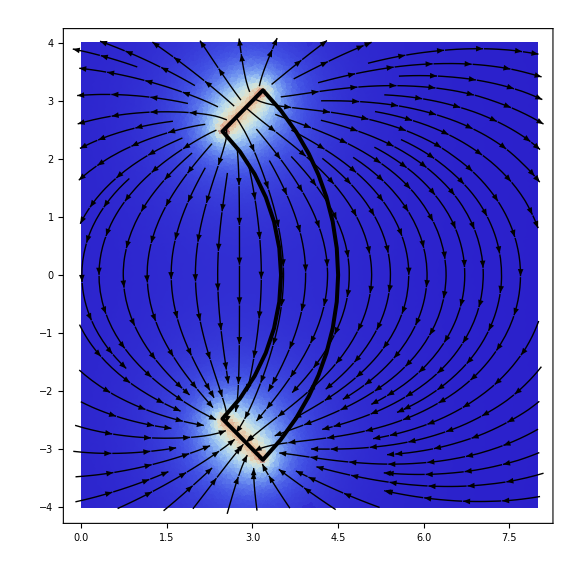

```mathematica
(* plot free current potential *)
segment=Show[
StreamDensityPlot[Evaluate@Hplot[x,y][[{1,2}]],{x,y}∈canvas,ColorFunction->ColorData["ThermometerColors"], StreamStyle->Black,StreamColorFunction->None,AspectRatio->Automatic],
RegionPlot[magnetSegmentBoundary,BoundaryStyle->{Thickness[0.005]}],
ImageSize->Large,Axes->False
]
```

```mathematica
Export["segment.jpg",segment]
```

segment.jpg